```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
Elements = Import["CrossHoleData/elements.txt","Table","FieldSeparators"->","];
Nodes = Import["CrossHoleData/nodes.txt","Table","FieldSeparators"->","];
Nodes = Drop[Nodes, None, {1}];(*odstrani prvi stolpec*)
Elements = Drop[Elements, None, {1}];
```

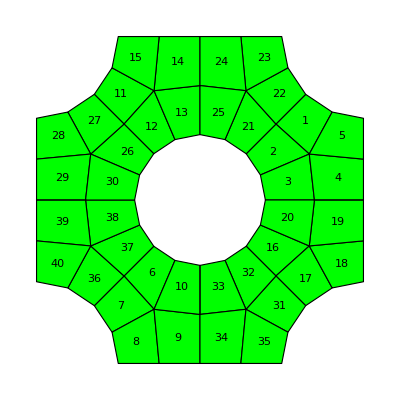

```mathematica
ELplot= Table[{
	Graphics[{
Green,EdgeForm[Black],Polygon[Nodes[[Elements[[i]]]]],Black,Text[ToString[i],Mean[Nodes[[Elements[[i]]]]]]
}]},
	{i,1,Length[Elements]}];
Show[ELplot]

 AreaEle= Table[
Area[Polygon[Nodes[[Elements[[i]]]]]],
	{i,1,Length[Elements]}];
```

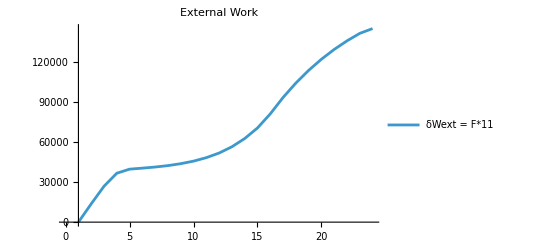

```mathematica
(*Import of data*)
(*Force:*)
ForceX = Import["CrossHoleData/FPx.txt", "Table", HeaderLines -> 4][[1;;-5,2]];
ForceY = Import["CrossHoleData/FPy.txt", "Table", HeaderLines -> 4][[1;;-5,2]];
(*Displacement*)
(*U1 = Import["CrossHoleData/U1.txt", "Table", HeaderLines -> 4][[1;;-5, 2]];
U2 = Import["CrossHoleData/U2.txt", "Table", HeaderLines -> 3][[1;;-5, 2]];

δWext1 = ForceX U1;
δWext2 = ForceY U2;
δWext3 = δWext1+δWext2;*)
(*Other data:*)
d = 0.8; (*thickness*)
u = 11; (*diformation of the edges?*)
δWext = 11*( ForceX + ForceY);

(*ListLinePlot[{δWext, δWext1, δWext2,δWext1+δWext2 }, AxesOrigin->{1,0}, PlotLegends->{"δWext = F*11","δWext1", "δWext2","δWext1 + δWext2"},PlotLabel->"External Work"]*)
ListLinePlot[{δWext}, AxesOrigin->{1,0}, PlotLegends->{"δWext = F*11","δWext1", "δWext2","δWext1 + δWext2"},PlotLabel->"External Work"]
```

```mathematica
(*Stress:*)
NAP = Import["CrossHoleData/Stress2.JSON","RawJSON"];
Keys[NAP[["0"]]];
```

```mathematica
(*Deformation gradient:*)

FJSON = Import["CrossHoleData/Grad_4elem_CH_2_PHANTOM.JSON", "RawJSON"];
Keys[FJSON[["0"]]];
```

```mathematica
Frames = Length[Keys[FJSON]];
nelements = Length[Keys[FJSON["1"]]];
ngp = Length[Keys[FJSON["1"][["1"]]]];
Δt = 1;(*1/(frames -1)*)

determinants = Table[{},{i,1,nelements}];
```

```mathematica
δWint = {};

For[frame = 0, frame <= Frames-1, frame++,
δWinte = 0;
Fframe = FJSON[ ToString[frame]];
For[ele=1, ele <= nelements, ele++,
(*Determinanta elementa*)
det = {};
Subscript[𝒯, 1] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,-1};
Subscript[𝒯, 2] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,-1};
Subscript[𝒯, 3] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {1,1};
Subscript[𝒯, 4] := {Subscript[𝓍, 1],Subscript[𝓎, 1]} = {-1,1};
Subscript[ψ, i_][𝒳_, 𝒴_] := 1/4(1 + Subscript[𝒯, i][[1]] * 𝒳) *(1 + Subscript[𝒯, i][[2]]  * 𝒴);
x = Nodes[[Elements[[ele]]]][[;;,1]];
y = Nodes[[Elements[[ele]]]][[;;,2]];

X[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] x[[i]],{i,1,4}];
Y[𝒳_, 𝒴_]  := Sum[Subscript[ψ, i][𝒳, 𝒴] y[[i]],{i,1,4}];
J[𝒳_, 𝒴_]  = ({{D[X[𝒳, 𝒴], 𝒳], D[Y[𝒳, 𝒴], 𝒳]}, {D[X[𝒳, 𝒴], 𝒴], D[Y[𝒳, 𝒴], 𝒴]}});

det = Append[det,
{Det[J[-1/(√3),-1/(√3)]],
Det[J[1/(√3),-1/(√3)]],
Det[J[-1/(√3),1/(√3)]],
Det[J[1/(√3),1/(√3)]]}];
determinants[[ele]] = Sum[det[[1,i]],{i,1,4}];

δWintgp = 0;
Fele = Fframe[ ToString[ele]];
For[gp = 1, gp < ngp, gp++,
(*deformation gradient F*)
F =  Fele[[ToString[gp]]][["F"]];

F11 = F[[1]];
F12 = F[[2]];
F21 = F[[3]];
F22 = F[[4]];
F33 = F[[5]]/d;

(*Stress*)
σ = NAP[[ToString[frame]]][[ToString[ele]]][[ToString[gp]]][["S"]];
(*σ -> S11, S22, S33, S12*)
σ11 =σ[[1]];
σ12 =σ[[4]]; (*Drugi stolpec*)
σ22 =σ[[2]];

(*velocity gradient δv -> Ḟ*)
Fdot =FJSON[ToString[Keys[FJSON][[-1]]]][ToString[ele]][ToString[gp]]["F"];
δvf = 1/Δt (Fdot - {1,1,1,1,1});
δv11 = δvf[[1]];
δv12 = δvf[[2]];
δv21 = δvf[[3]];
δv22 = δvf[[4]];
δv33 = δvf[[5]];

(*1.st Piola Kirchoff Stress p*)
p11 = F33 (F22 σ11 - F12 σ12);
p12 = - F21 F33 σ11 + F11 F33 σ12;
p21 = F33 (F22 σ12 - F12 σ22);
p22 = -F21 F22 σ12 + F11 F33 σ22;

δW = (p11 δv11 + p12 δv12 + p21 δv21 + p22 δv22) *det[[1,gp]] * d;(*t -> Thickness*)
δWintgp += δW; (*Sum dela vseh gaussovih tock*)

];(*gp*)
δWinte += δWintgp;
];(*ele*)
δWint = Append[δWint, δWinte];
];(*frames*)
```

```mathematica
δWint
```

{0.,12829.7,24485.6,19699.,14589.1,15951.2,17481.9,19056.7,20680.2,22032.5,23607.3,25378.1,29698.6,40331.8,50386.2,59280.5,68306.8,75149.1,80150.4,83633.1,85863.6,87050.1,87349.9,87102.2}

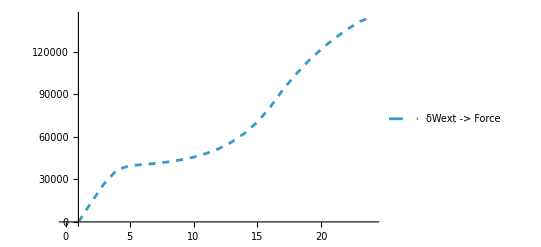

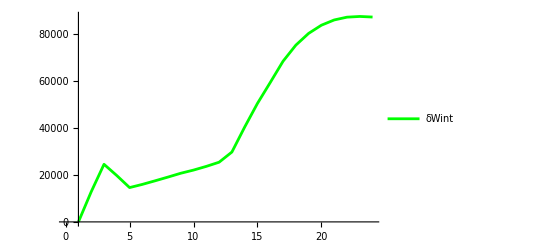

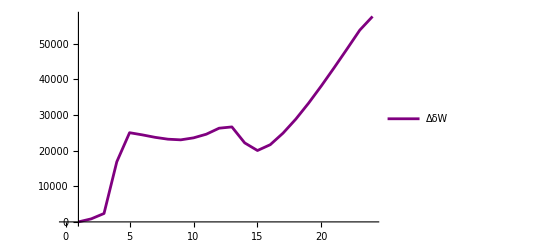

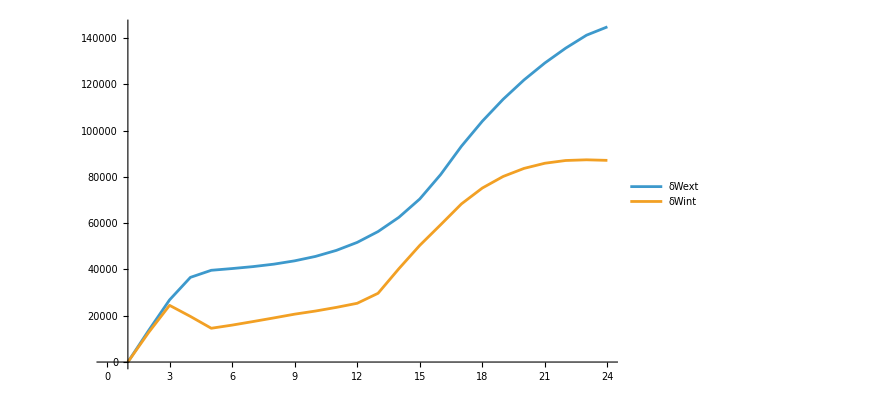

```mathematica
P1 = ListLinePlot[{δWext},AxesOrigin->{1,0}, PlotLegends->{"δWext -> Force"}, PlotStyle->Dashed]
(*P2 = ListLinePlot[{ δWext3},AxesOrigin->{1,0}, PlotLegends->{"δWext3 -> U1F1 + U2F2"}, PlotStyle->{Normal, Blue}]*)
P3 = ListLinePlot[{ δWint},AxesOrigin->{1,0}, PlotLegends->{"δWint"}, PlotStyle->Green]
P4 = ListLinePlot[{(δWext - δWint)},AxesOrigin->{1,0}, PlotLegends->{"ΔδW"}, PlotStyle->Purple]
P4 = ListLinePlot[{δWext ,δWint},AxesOrigin->{1,0}, PlotLegends->{"δWext","δWint"}]
```

```mathematica
δWext -  δWint
```

{0.,854.341,2359.63,16876.,25039.7,24427.5,23734.4,23217.5,23033.5,23591.2,24617.5,26302.6,26660.2,22180.4,20037.7,21671.4,24917.3,28859.3,33346.2,38206.7,43300.8,48529.1,53829.2,57668.8}

```mathematica
(δWext -  δWint)/(δWint + 10^-16)
```

{0.,0.0665909,0.0963678,0.856698,1.71633,1.53138,1.35766,1.21834,1.11379,1.07075,1.04279,1.03643,0.897692,0.549949,0.397683,0.365574,0.364786,0.384027,0.416045,0.456838,0.504298,0.557485,0.616248,0.662082}

```mathematica
AreaEle
```

{39.7779,37.607,41.8808,52.2512,42.9205,37.607,39.7779,42.9205,52.2512,41.8808,39.7779,37.607,41.8808,52.2512,42.9205,37.607,39.7779,42.9205,52.2512,41.8808,37.607,39.7779,42.9205,52.2512,41.8808,37.607,39.7779,42.9205,52.2512,41.8808,39.7779,37.607,41.8808,52.2512,42.9205,39.7779,37.607,41.8808,52.2512,42.9205}

```mathematica
determinants
```

{39.777919769247223,37.606958346726467,41.88076065922665,52.2512369,42.92049457930781,37.606958346726467,39.777919769247223,42.92049457930781,52.2512369,41.88076065922665,39.777919769247223,37.606958346726467,41.88076065922665,52.2512369,42.92049457930781,37.606958346726467,39.777919769247223,42.92049457930781,52.2512369,41.88076065922665,37.606958346726467,39.777919769247223,42.92049457930781,52.2512369,41.88076065922665,37.606958346726467,39.777919769247223,42.92049457930781,52.2512369,41.88076065922665,39.777919769247223,37.606958346726467,41.88076065922665,52.2512369,42.92049457930781,39.777919769247223,37.606958346726467,41.88076065922665,52.2512369,42.92049457930781}

```mathematica
AreaEle - determinants
```

{7.10543×10^-15,7.10543×10^-15,0.,0.,7.10543×10^-15,7.10543×10^-15,7.10543×10^-15,0.,0.,-7.10543×10^-15,7.10543×10^-15,7.10543×10^-15,0.,0.,0.,7.10543×10^-15,7.10543×10^-15,0.,0.,0.,0.,7.10543×10^-15,0.,0.,0.,7.10543×10^-15,0.,0.,0.,0.,7.10543×10^-15,0.,0.,0.,0.,0.,7.10543×10^-15,0.,0.,0.}

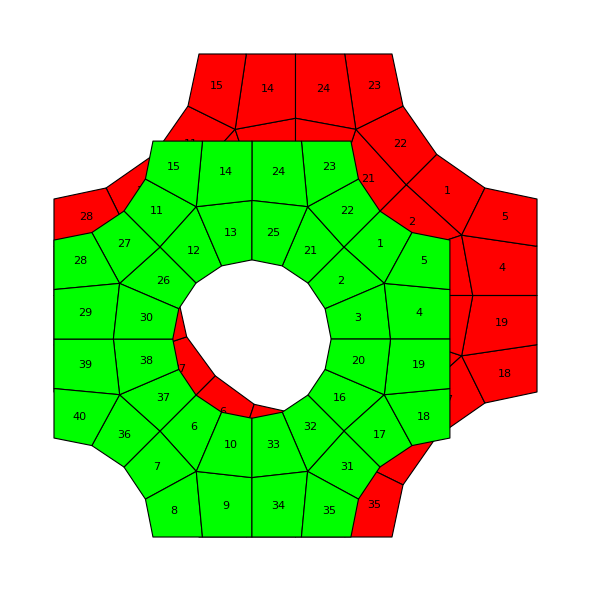

```mathematica
DefNodes = Import["CrossHoleData/DeformedNodes.csv","Table","FieldSeparators"->","];

 ELDEFplot= Table[{
	Graphics[{
Red,EdgeForm[Black],Polygon[DefNodes[[Elements[[i]]]]],Black,Text[ToString[i],Mean[DefNodes[[Elements[[i]]]]]]
}]},
	{i,1,Length[Elements]}];
Show[ELDEFplot, ELplot]
```

```mathematica
AreaDefEle= Table[
Area[Polygon[DefNodes[[Elements[[i]]]]]],
	{i,1,Length[Elements]}];
```

```mathematica
Total@AreaEle - Total@AreaDefEle
```

-342.464

```mathematica
Vnd = Total@AreaEle * d;
d2 = Vnd/(Total@AreaDefEle)
```

0.666872

```mathematica
AreaDefEle / AreaEle // MatrixForm
```

(1.25891
1.27166
1.16468
1.15773
1.16669
1.27166
1.25891
1.16669
1.15773
1.16468
1.25891
1.27166
1.16468
1.15773
1.16669
1.27166
1.25891
1.16669
1.15773
1.16468
1.27166
1.25891
1.16669
1.15773
1.16468
1.27166
1.25891
1.16669
1.15773
1.16468
1.25891
1.27166
1.16468
1.15773
1.16669
1.25891
1.27166
1.16468
1.15773
1.16669)